```mathematica
Ueff[x_,y_,m_]:=(
-(1-m)/Sqrt[(x-(-m))^2+y^2]
-m/Sqrt[(x-(1-m))^2+y^2]
-(x^2+y^2)/2)
```

```mathematica
dUx[x_,y_,m_]:=-x+(m (-1+m+x))/(((-1+m+x)^2+y^2)^(3/2))-((-1+m) (m+x))/(((m+x)^2+y^2)^(3/2))
dUy[x_,y_,m_]:=y (-1+m/(((-1+m+x)^2+y^2)^(3/2))+(1-m)/(((m+x)^2+y^2)^(3/2)))
```

```mathematica
next[{x_,y_,vx_,vy_},dt_,m_]:={
x+dt vx,
y+dt vy,
vx+dt(-dUx[x,y,m]+2vy),
vy+dt(-dUy[x,y,m]-2vx)
}
```

```mathematica
Clear[state];
m=.02;
state[0]={.42,.9,0.,0.};
state[i_]:=state[i]=next[state[i-1],.01,m]
```

```mathematica
stats=state/@Range[30000];
```

```mathematica
pts=#[[1;;2]]&/@stats;
```

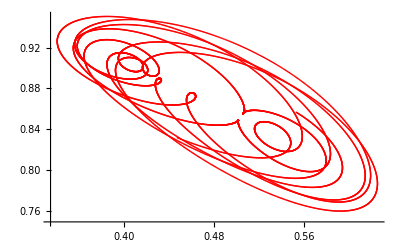

```mathematica
ListPlot[pts[[10000;;20000]],PlotStyle->Red]
```

-1.49247

-1.4902

0.00226872

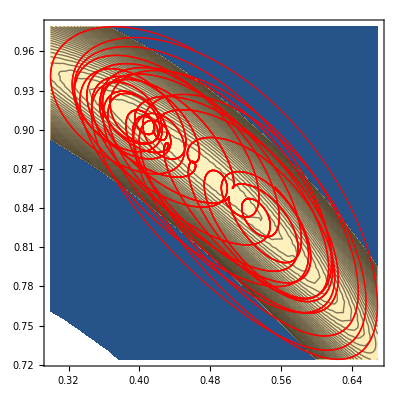

```mathematica
Umin=Ueff[Min[#[[1]]&/@pts],Max[#[[2]]&/@pts],m]
Umax=Ueff[1/2-m,Sqrt[3]/2,m]
Udiff=Umax-Umin
Show[ContourPlot[Ueff[x,y,m],
{x,Min[#[[1]]&/@pts],Max[#[[1]]&/@pts]},
{y,Min[#[[2]]&/@pts],Max[#[[2]]&/@pts]},Contours->Range[Umax-2*Udiff,Umax,Udiff/20]],ListPlot[pts[[-20000;;]],PlotStyle->Red]]
```

```mathematica
Ueff[2,2,.01]
```

-0.973931

```mathematica
NMaximize[Ueff[x,y,1/10],{x,y}]
```

{-1.455,{x→0.4,y→0.866025}}

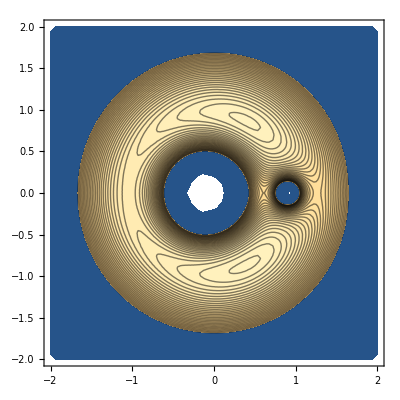

```mathematica
ContourPlot[Ueff[x,y,.1],{x,-2,2},{y,-2,2},Contours->Range[-2,-1.46,.02]]
```

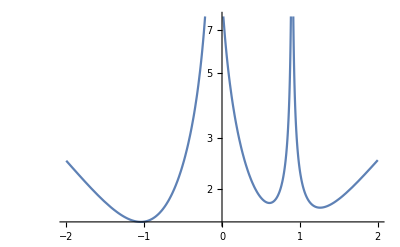

```mathematica
LogPlot[-Ueff[x,0,.1],{x,-2,2}]
```

```mathematica
Maximize[Ueff[x,y,m],{x,y}]
```

$Aborted

```mathematica
D[Ueff[x,y,m],x]/.{x->1/2-m,y->Sqrt[3]/2}//Simplify
```

0

```mathematica
D[Ueff[x,y,m],y]/.{x->1/2-m,y->Sqrt[3]/2}//Simplify
```

0

```mathematica
Solve[D[Ueff[x,0,1/10],x]==0,x]
```

{{x→Root1.26Root[-7300+16081 #1-8560 #1^2+4600 #1^3-16000 #1^4+10000 #1^5&,1]1.2596998329023315},{x→Root0.609Root[-7280+16481 #1-6560 #1^2+4600 #1^3-16000 #1^4+10000 #1^5&,1]0.6090351100232024},{x→Root-1.04Root[7300-15919 #1+11440 #1^2+4600 #1^3-16000 #1^4+10000 #1^5&,1]-1.04160890857106}}